```mathematica
(*Problem 3b*)
(*Begin by creating the characteristic polynomials:*)
```

```mathematica
p[z_]:=z^3-1/3 z^2-1/3 z-1/3;
σ[z_]:=23/12 z^2-2/12 z+3/12;
```

```mathematica
(*Let z = e^iθ and find λΔt:*)
```

```mathematica
pts=Table[p[Exp[I θ]]/σ[Exp[I θ]],{θ,0,2π,0.001}]
```

{5.55112×10^-17+0. ⅈ,7.64885×10^-14+0.001 ⅈ,1.2222×10^-12+0.002 ⅈ,6278,1.74225×10^-12-0.00218531 ⅈ,1.50736×10^-13-0.00118531 ⅈ,1.70694×10^-16-0.000185307 ⅈ}
 |  |  |  |

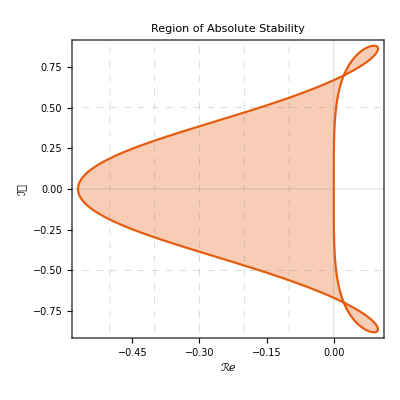

```mathematica
ComplexListPlot[pts,Joined->True,PlotTheme->"Scientific",FrameLabel->{Style["ℛℯ",13,Bold,Black],Style["ℐ𝓂",13,Bold,Black]},PlotLabel->Style["Region of Absolute Stability",Black,13,Bold],GridLines->{{{-.5,Dashed},{-.4,Dashed},{-.3,Dashed},{-.2,Dashed},{-.1,Dashed},{0,Thick}},{{-.5,Dashed},{0,Thick},{.5,Dashed}}},AspectRatio->1,Filling->Axis]
```

```mathematica
(*Problem 2b*)
(*Create a matrix from the Butcher Array*)
```

```mathematica
A={{0,0,0},{1/4,1/4,0},{0,1,0}};
```

```mathematica
(*Create a matrix from the b-vector and h-vectors*)
```

```mathematica
b={1/6,2/3,1/6};
h={1,1,1};
```

```mathematica
hbt=Outer[Times,h,b];
```

```mathematica
(*Verify the outputs:*)
```

```mathematica
hbt//MatrixForm
A//MatrixForm
hbt-A//MatrixForm
```

(1/6 | 2/3 | 1/6
1/6 | 2/3 | 1/6
1/6 | 2/3 | 1/6)

(0 | 0 | 0
1/4 | 1/4 | 0
0 | 1 | 0)

(1/6 | 2/3 | 1/6
-1/12 | 5/12 | 1/6
1/6 | -1/3 | 1/6)

```mathematica
(*Generate the matrix whose roots will be analyzed*)
```

```mathematica
S[z_]:=IdentityMatrix[3]+z*(hbt-A)
```

```mathematica
(*Compute the roots of the determinant <=1 and plot them*)
```

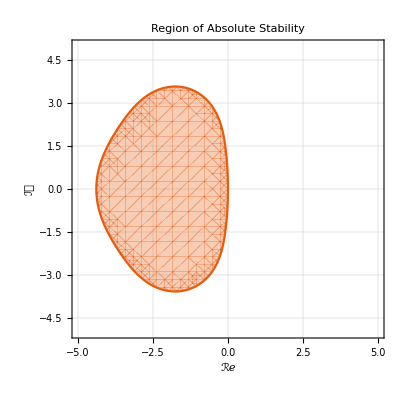

```mathematica
ComplexRegionPlot[
Abs[Det[S[z]]]<=1,
{z,-5-5I,5+5I},
GridLines->Automatic,
GridLinesStyle->Directive[Gray, Dashed],
PlotTheme->"Scientific",
FrameLabel->{Style["ℛℯ",13,Bold,Black],Style["ℐ𝓂",13,Bold,Black]},PlotLabel->Style["Region of Absolute Stability",Black,13,Bold]
]
```

```mathematica
(*Problem 2c*)
(*Create the matrix B*)
B={{-1,3,-5,7},{0,-2,4,-6},{0,0,-4,6},{0,0,0,-16}};
```

```mathematica
B//MatrixForm
```

(-1 | 3 | -5 | 7
0 | -2 | 4 | -6
0 | 0 | -4 | 6
0 | 0 | 0 | -16)

```mathematica
(*Get the eigenvalues:*)
```

```mathematica
eigs=Table[{Eigenvalues[B][[i]],0},{i,4}]
```

{{-16,0},{-4,0},{-2,0},{-1,0}}

```mathematica
eigplt=ListPlot[
eigs->{"λ_1","λ_2","λ_3","λ_4"},
PlotTheme->"Scientific",FrameLabel->{Style["ℛℯ",13,Bold,Black],Style["ℐ𝓂",13,Bold,Black]},
AspectRatio->1]
```

-Graphics-

```mathematica
t[z_]:=6(z-1)/(z^2+4z+1)
```

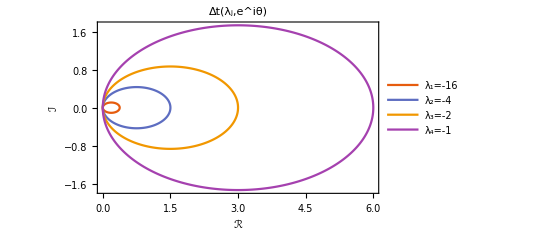

```mathematica
ComplexListPlot[
Table[
Table[t[Exp[I θ]]/Abs[Eigenvalues[B][[i]]],{θ,0,2π,0.001}],
{i,1,4}],
Joined->True,AxesLabel->{Style["ℛ",Medium,Bold],Style["ℐ",Medium,Bold]},PlotLegends->{"λ_1="<>ToString[Eigenvalues[B][[1]]],"λ_2="<>ToString[Eigenvalues[B][[2]]],
"λ_3="<>ToString[Eigenvalues[B][[3]]],"λ_4="<>ToString[Eigenvalues[B][[4]]]},PlotLabel->Style["Δt(λ_j,e^iθ)",FontSize->18,Black],
PlotTheme->"Scientific",
GridLines->{{3/8,0,3/2,3,6},{0}}]
```

```mathematica
t[Exp[I π]]/16
```

3/8

```mathematica
k2fac[dt_]:=Inverse[IdentityMatrix[4]-dt/4*B]
```

```mathematica
k2fac[3/8-0.0001]//MatrixForm
```

(0.914307 | 0.216498 | -0.252602 | 0.134444
0. | 0.842141 | 0.22963 | -0.1378
0. | 0. | 0.727326 | 0.163631
0. | 0. | 0. | 0.400064)

```mathematica
B//MatrixForm
```

(-1 | 3 | -5 | 7
0 | -2 | 4 | -6
0 | 0 | -4 | 6
0 | 0 | 0 | -16)

```mathematica
system[y_]:=SetPrecision[B.y,40];
```

```mathematica
K1[y_,dt_]:=SetPrecision[system[y],40];
K2[y_,dt_]:=SetPrecision[k2fac[dt].system[y+dt/4*K1[y,dt]],40];
K3[y_,dt_]:=SetPrecision[system[y+dt*K2[y,dt]],40];
```

```mathematica
method[y_,dt_]:=y+dt/6*(K1[y,dt]+4*K2[y,dt]+K3[y,dt]);
```

```mathematica
y0={1,1,1,1};
```

```mathematica
K2[y0,dtm]
```

{-3.690228440425796114443252183559106239227,2.5514957721423971767991084612103491505,-4.287143750558384667997596735518816829033,2.991869918699186804007472864009466287863}

```mathematica
tol=SetPrecision[0.0001,40];
dtp=SetPrecision[0.375+tol,40];
dtm=SetPrecision[0.375-tol,40];
```

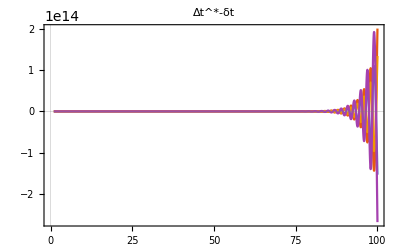

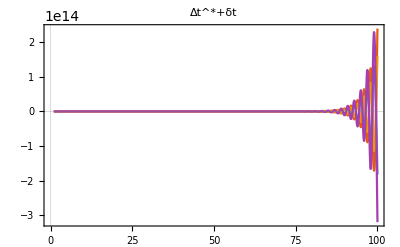

```mathematica
yps={};
yms={};
y0={1,1,1,1};
Do[AppendTo[yps,y0];y0=SetPrecision[method[y0,dtp],40],100]
y0={1,1,1,1};
Do[AppendTo[yms,y0];y0=SetPrecision[method[y0,dtm],40],100]
llp1=ListLinePlot[Table[yms[[All,i]],{i,4}],PlotRange->Full,InterpolationOrder->2,PlotTheme->"Scientific",PlotLabel->"Δt^*-δt"]
llp2=ListLinePlot[Table[yps[[All,i]],{i,4}],PlotRange->Full,InterpolationOrder->2,PlotTheme->"Scientific",PlotLabel->"Δt^*+δt"]
```